```mathematica
Data = Import["/Users/eohomegrownapps/CODE/Assorted codings/Wolfram/Accelerometer 2.csv","Data"];
```

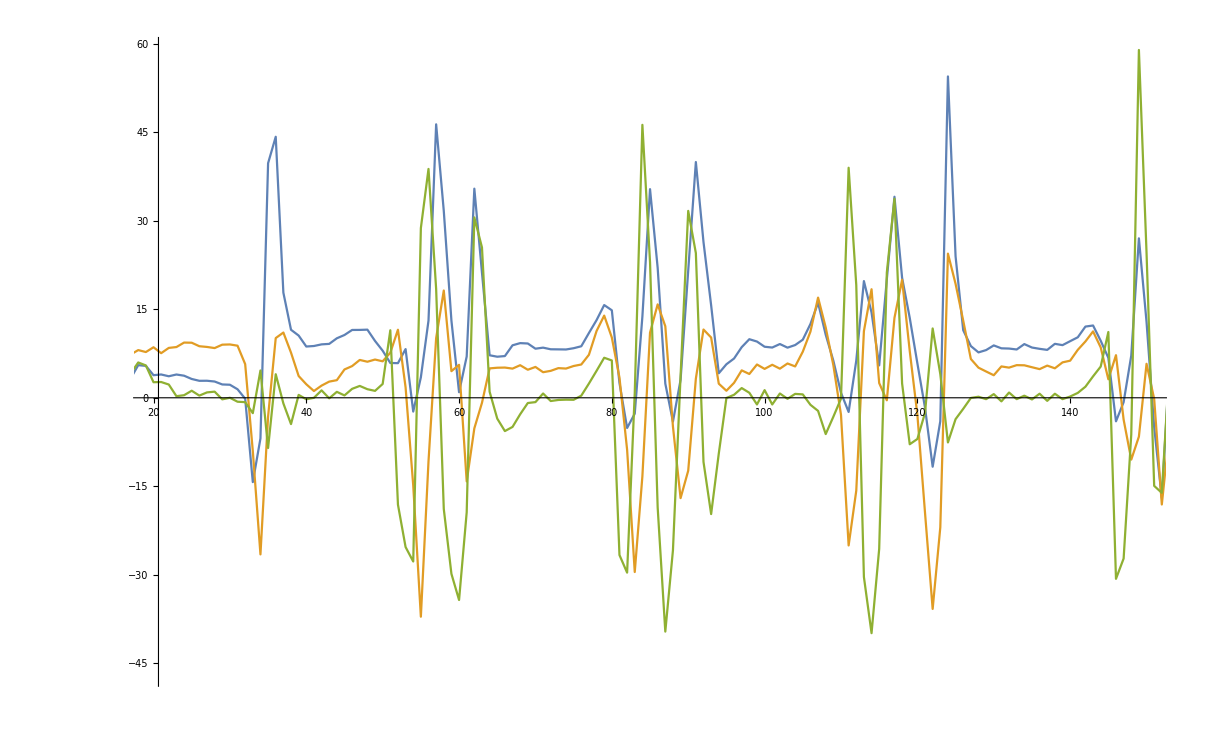

```mathematica
ListLinePlot[{Data[[All,2]],Data[[All,3]],Data[[All,4]]},PlotRange->{{20,150},Full}]
```

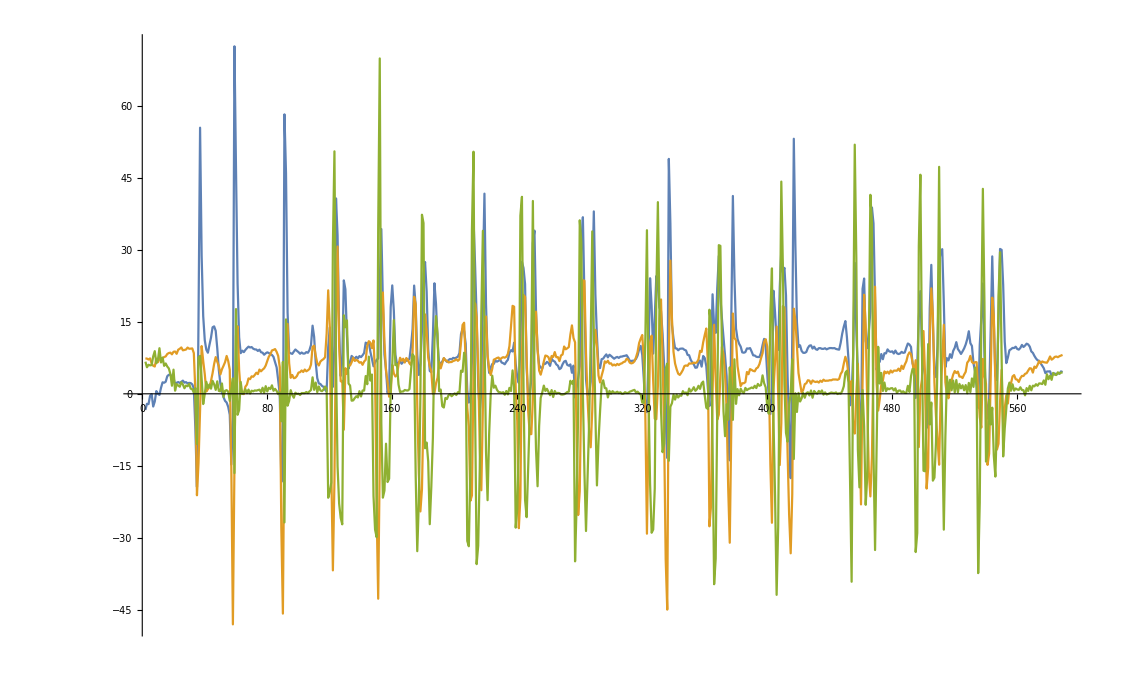

```mathematica
DateListPlot[Data]
```

DateListPlot::dtvals: Unable to automatically determine horizontal coordinates for the given data and DataRange.

DateListPlot::ldata: {{Milliseconds,X,Y,Z},{1,-3.35472,7.39227,6.69946},{51,-2.08685,7.33952,5.53505},{101,-2.15384,7.14761,6.0531},«43»,{2301,9.48662,6.68706,2.60263},{2351,4.96057,5.80429,0.606476},{2401,2.05165,4.04359,0.516174},«539»} is not a valid dataset or list of datasets.

```mathematica
Data = Import["/Users/eohomegrownapps/CODE/Assorted codings/Wolfram/Accelerometer 3.csv","Data"];
```

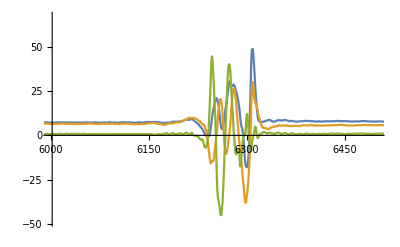

```mathematica
ListLinePlot[{Data[[All,2]],Data[[All,3]],Data[[All,4]]},PlotRange->{{6000,6500},Full}]
```

```mathematica
q = Table[Part[Data,n;;n+120],{n,200,9700,500}]
```

{{{1980,2.85542,8.80757,0.625504},{1990,2.84108,8.9227,0.554215},{2000,2.84586,9.01866,0.435394},{2010,2.80759,9.15299,0.378357},{2021,2.72147,9.3113,0.216766},111,{3140,4.39122,7.61777,0.79184},{3150,4.57303,7.67055,1.10077},{3160,4.72134,7.7809,1.12453},{3170,4.90794,7.95839,0.948685},{3181,5.06105,8.12631,0.820358}},18,{1}}
 |  |  |  |

```mathematica
Monitor[Rasterize/@Table[ListLinePlot[{q[[n]][[All,2]],q[[n]][[All,3]],q[[n]][[All,4]]},PlotRange->All,Axes->None,AxesLabel->None,PlotStyle->{Red, Green, Blue}],{n,1,Length[q]}],n]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

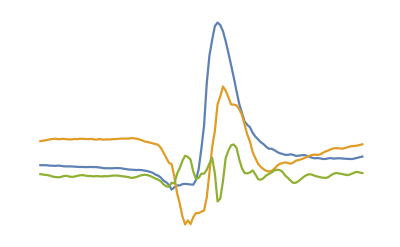
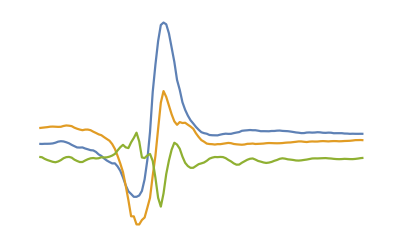
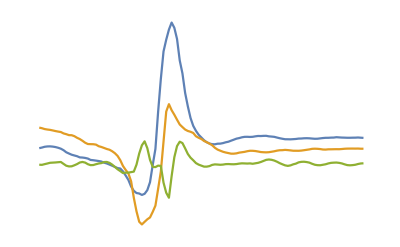
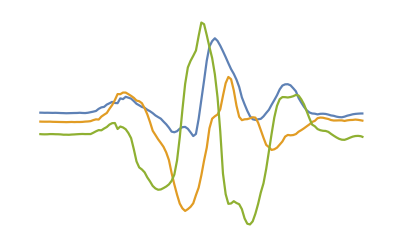
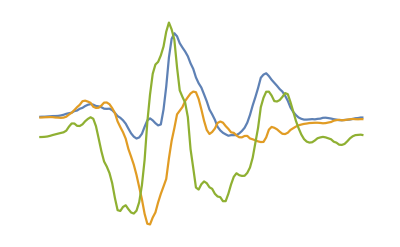
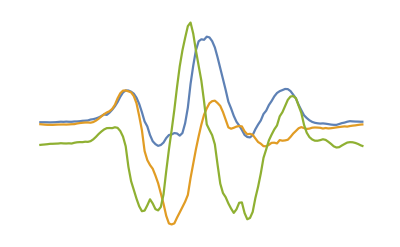
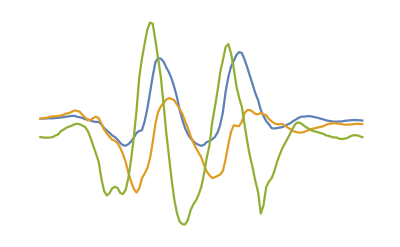
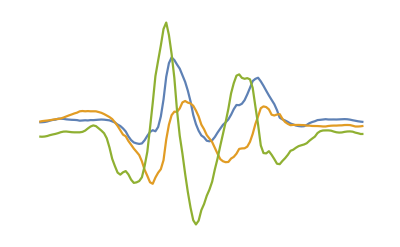
```mathematica
l=<|-Graphics-->1,-Graphics-->1,-Graphics-->1,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->3,-Graphics-->3,-Graphics-->3,-Graphics-->4,-Graphics-->4,-Graphics-->4,-Graphics-->5,-Graphics-->5,-Graphics-->5|>
```

<|-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→5,-Graphics-→5,-Graphics-→5|>

```mathematica
Map[Rasterize[Keys[#]]->Values[#]&,l]
```

Keys::invrl: The argument 1 is not a valid Association or a list of rules.

Values::invrl: The argument 1 is not a valid Association or a list of rules.

Keys::invrl: The argument 1 is not a valid Association or a list of rules.

Values::invrl: The argument 1 is not a valid Association or a list of rules.

Keys::invrl: The argument 1 is not a valid Association or a list of rules.

General::stop: Further output of Keys::invrl will be suppressed during this calculation.

Values::invrl: The argument 1 is not a valid Association or a list of rules.

General::stop: Further output of Values::invrl will be suppressed during this calculation.

<|-Graphics-→-Graphics-→Values[1],-Graphics-→-Graphics-→Values[1],-Graphics-→-Graphics-→Values[1],-Graphics-→-Graphics-→Values[2],-Graphics-→-Graphics-→Values[2],-Graphics-→-Graphics-→Values[2],-Graphics-→-Graphics-→Values[3],-Graphics-→-Graphics-→Values[3],-Graphics-→-Graphics-→Values[3],-Graphics-→-Graphics-→Values[4],-Graphics-→-Graphics-→Values[4],-Graphics-→-Graphics-→Values[4],-Graphics-→-Graphics-→Values[5],-Graphics-→-Graphics-→Values[5],-Graphics-→-Graphics-→Values[5]|>

```mathematica
Keys[l][[1]]
```

-Graphics-

```mathematica
Table[Rasterize[(Keys[l])[[a]]],(Values[l])[[a]],{a,1,Length[l],1}]
```

Part::pkspec1: The expression a cannot be used as a part specification.

Table::nliter: Non-list iterator Values[l]⟦a⟧ at position 2 does not evaluate to a real numeric value.

Table[Rasterize[Keys[l]⟦a⟧],Values[l]⟦a⟧,{a,1,Length[l],1}]